```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/Moat-meanfield/MF_DR/renorm_finitep_v2/specfun/mu320T30/input_data

```mathematica
Re1=Import["./RedataT30mu320.dat"];
Im1=Import["./ImdataT30mu320.dat"];
Im2=Im1;
Re2=Re1;
spec=-1/π*Im2/(Re2^2+Im2^2);
```

```mathematica
Dimensions[Im1]
```

{201,1}

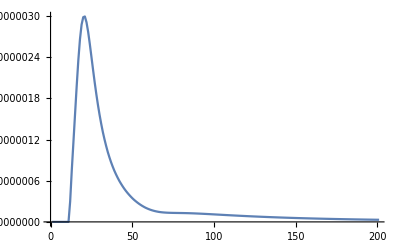

```mathematica
ListLinePlot[Flatten[spec],PlotRange->{{0,200},All},ScalingFunctions->Automatic]
```

```mathematica
specdata=Table[{1+(i-1)*10,Flatten[spec][[i]]},{i,1,Length[spec]}];
```

```mathematica
Export["./spec_data.dat",specdata]
```

./spec_data.dat

```mathematica
Ep=Sqrt[Flatten[Import["./Ep.dat"]]];
ps=Table[1+(i-1)*20,{i,1,Length[Ep]}];
Epdata=Table[{ps[[i]],Ep[[i]]},{i,1,Length[Ep]}];
Export["./Ep_data.dat",Epdata]
```

./Ep_data.dat